## Vector addition and vector (and scalar) sign figures: VectorsWithOppositeOrientationFig1.eps, vectorAdditionFig1.eps, scalarOrientationFig1.eps

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

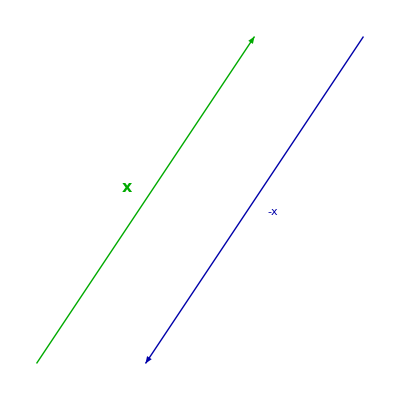

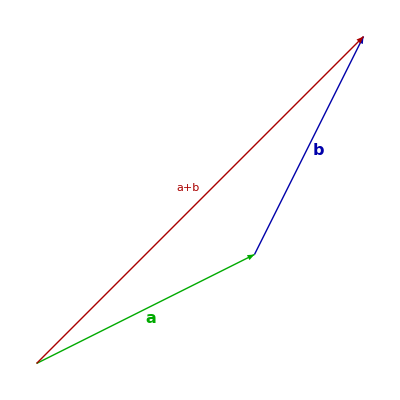

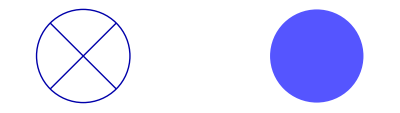

```mathematica
ClearAll[e1,e2,bold, fs, o]

bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;

(*{e1,e2,e3}= IdentityMatrix[3];*)
{e1,e2}= IdentityMatrix[2];
o = {0,0};

ClearAll[clk, ctr, rp, rn]
ctr =RotationTransform[Pi/2];
clk =RotationTransform[-Pi/2];
rp = ctr[#//Normalize] &;
rn = clk[#//Normalize] &;

p1 = Module[{x0,x1,y0, y1},
x0 = o;
x1 = e1+1.5e2;
y0 = 1.5 e1+1.5e2;
y1 = e1/2;
Graphics[ {
Thick,
Arrowheads[0.05],
Green // Darker,
Arrow[{x0,x1}],
Text["x"//bold//fs,  (x0+x1)/2 + 0.1 rp[x1-x0]],
Blue // Darker,
Arrow[{y0, y1} ],
Text[Row[{"-"//fs,"x"//bold//fs}],  (y0+y1)/2 + 0.1 rp[y1-y0]]
}]
]

p2 = Module[{v1,v2,vs},
v1 = e1 + 0.5e2;
v2 = 0.5 e1 + e2;
vs = v1 + v2;

Graphics[ {
Thick,
Arrowheads[0.05],
Green // Darker,
Arrow[{o,v1}],
Text["a"//bold//fs, v1/2+0.05 rn[v1] ],
Blue // Darker,
Arrow[{v1,vs} ],
Text["b"//bold//fs, v1 + v2/2+0.05 rn[v2]],
Red // Darker,
Arrow[{o,vs} ],
Text[Row[{
"a"//bold//fs,
"+" // fs,
"b"//bold//fs}]
, vs/2 + 0.08rp[vs]]
}]
]

p3 = Module[{p1, p2,r},
r = 0.01;
p1 = r(e1+e2)/Sqrt[2];
p2 = r(e1-e2) /Sqrt[2];
Graphics[ {
Thick,
Blue//Darker,
Circle[o,r],

Line[{-p1, p1}],
Line[{-p2,p2}],
Blue// Lighter,
Disk[0.05 e1,r]
}]
]
```

```mathematica
peeters`exportForLatex["VectorsWithOppositeOrientationFig1", p1]
peeters`exportForLatex["vectorAdditionFig1", p2]
peeters`exportForLatex["scalarOrientationFig1", p3]
```

{VectorsWithOppositeOrientationFig1.eps,VectorsWithOppositeOrientationFig1pn.png}

{vectorAdditionFig1.eps,vectorAdditionFig1pn.png}

{scalarOrientationFig1.eps,scalarOrientationFig1pn.png}